```mathematica
RadioButtonBar[
Dynamic[fileName],
{
"~/Downloads/optimizerHistory.json",
"/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json"
},Appearance->"Vertical"]

raw=Import[fileName];
```

| ~/Downloads/optimizerHistory.json
 | /Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json

```mathematica
raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];
```

```mathematica
(*Optional: Drop rows with non-numeric values*)
Length[raw]
raw = Select[raw,AllTrue[Values[#],NumericQ]&];
Length[raw]
```

436

436

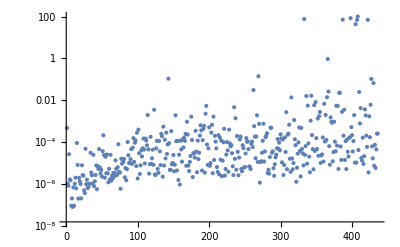

```mathematica
ListLogPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->All,
Joined->False
]
```

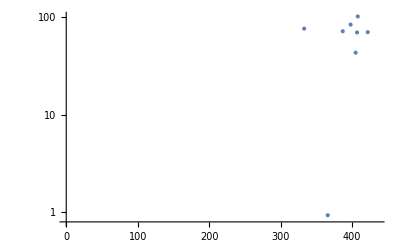

```mathematica
ListLogPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->{0.8,All},
Joined->False
]
```

```mathematica
bestCase = MaximalBy[raw,#["maximizeMe"]&][[1]]
```

<|L0BPhaseSet→-1.91682,L1PhaseSet→-19.752,L2PhaseSet→-38.8928,L3PhaseSet→-0.0680297,S1EL_xOffset→0.000415489,S1EL_yOffset→-0.000220904,S2EL_xOffset→-0.00142159,S2EL_yOffset→0.0000216812,S2ER_xOffset→-0.00228295,S2ER_yOffset→-0.000489676,S1ER_xOffset→0.000901706,S1ER_yOffset→0.000233506,XC1FFkG→0.207037,XC3FFkG→-0.09037,YC1FFkG→-0.00218319,YC2FFkG→-0.00520243,PDrive_mean_x→3.2142×10^-6,PDrive_mean_y→-1.1471×10^-6,PDrive_sigma_x→0.0000430154,PDrive_sigma_y→0.0000254369,PDrive_mean_xp→0.000797803,PDrive_mean_yp→-0.0000769295,PDrive_median_x→-2.9537×10^-6,PDrive_median_y→-1.3117×10^-6,PDrive_median_xp→0.000970304,PDrive_median_yp→-0.0000783731,PDrive_sigmaSI90_x→0.0000286675,PDrive_sigmaSI90_y→0.0000250725,PDrive_sigmaSI90_z→0.0000233094,PDrive_emitSI90_x→0.000156064,PDrive_emitSI90_y→0.0000148619,PDrive_zCentroid→991.332,PWitness_mean_x→-3.067×10^-6,PWitness_mean_y→3.3647×10^-6,PWitness_sigma_x→0.0000347497,PWitness_sigma_y→0.0000180011,PWitness_mean_xp→0.000884182,PWitness_mean_yp→-0.000125811,PWitness_median_x→1.1675×10^-6,PWitness_median_y→2.5197×10^-6,PWitness_median_xp→0.00087884,PWitness_median_yp→-0.000126756,PWitness_sigmaSI90_x→0.0000302083,PWitness_sigmaSI90_y→0.0000169199,PWitness_sigmaSI90_z→0.0000108153,PWitness_emitSI90_x→0.0000166824,PWitness_emitSI90_y→3.5934×10^-6,PWitness_zCentroid→991.332,bunchSpacing→0.000196628,transverseCentroidOffset→7.7337×10^-6,lostChargeFraction→0.0000119933,errorTerm_lostChargeFraction→0.,errorTerm_bunchSpacing→0.,errorTerm_transverseOffset→0.,errorTerm_angleOffset→0.,errorTerm_mainObjective→0.058628,maximizeMe→102.34|>

```mathematica
(*Format for yml*)
string = ""
Do[
string = string<>key<>" : "<>ToString[bestCase[key],CForm]<>"\n",
{key,Keys[bestCase]}
]
string
```

L0BPhaseSet : -1.9168247346
L1PhaseSet : -19.7519882334
L2PhaseSet : -38.892824709
L3PhaseSet : -0.0680297215
S1EL_xOffset : 0.0004154894
S1EL_yOffset : -0.000220904
S2EL_xOffset : -0.0014215916
S2EL_yOffset : 0.0000216812
S2ER_xOffset : -0.0022829539
S2ER_yOffset : -0.0004896763
S1ER_xOffset : 0.0009017061
S1ER_yOffset : 0.0002335062
XC1FFkG : 0.2070371508
XC3FFkG : -0.090370049
YC1FFkG : -0.0021831925
YC2FFkG : -0.0052024344
PDrive_mean_x : 3.2142e-6
PDrive_mean_y : -1.1471e-6
PDrive_sigma_x : 0.0000430154
PDrive_sigma_y : 0.0000254369
PDrive_mean_xp : 0.0007978032
PDrive_mean_yp : -0.0000769295
PDrive_median_x : -2.9537e-6
PDrive_median_y : -1.3117e-6
PDrive_median_xp : 0.0009703036
PDrive_median_yp : -0.0000783731
PDrive_sigmaSI90_x : 0.0000286675
PDrive_sigmaSI90_y : 0.0000250725
PDrive_sigmaSI90_z : 0.0000233094
PDrive_emitSI90_x : 0.0001560636
PDrive_emitSI90_y : 0.0000148619
PDrive_zCentroid : 991.3316808106
PWitness_mean_x : -3.067e-6
PWitness_mean_y : 3.3647e-6
PWitness_sigma_x : 0.0000347497
PWitness_sigma_y : 0.0000180011
PWitness_mean_xp : 0.0008841821
PWitness_mean_yp : -0.0001258106
PWitness_median_x : 1.1675e-6
PWitness_median_y : 2.5197e-6
PWitness_median_xp : 0.0008788397
PWitness_median_yp : -0.0001267557
PWitness_sigmaSI90_x : 0.0000302083
PWitness_sigmaSI90_y : 0.0000169199
PWitness_sigmaSI90_z : 0.0000108153
PWitness_emitSI90_x : 0.0000166824
PWitness_emitSI90_y : 3.5934e-6
PWitness_zCentroid : 991.3318774385
bunchSpacing : 0.0001966278
transverseCentroidOffset : 7.7337e-6
lostChargeFraction : 0.0000119933
errorTerm_lostChargeFraction : 0.
errorTerm_bunchSpacing : 0.
errorTerm_transverseOffset : 0.
errorTerm_angleOffset : 0.
errorTerm_mainObjective : 0.0586279555
maximizeMe : 102.3402564637

```mathematica
Norm[{bestCase["PDrive_mean_x"],bestCase["PDrive_mean_y"]}-{bestCase["PWitness_mean_x"],bestCase["PWitness_mean_y"]}]
```

7.73368×10^-6

## Plot all

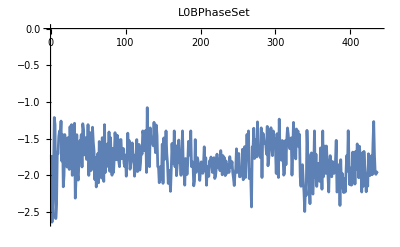
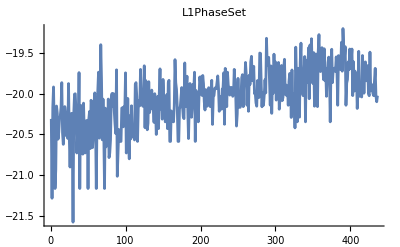
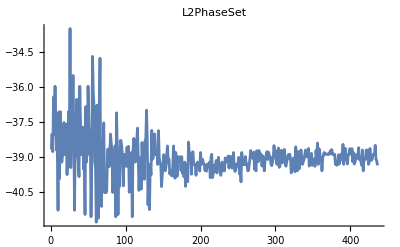
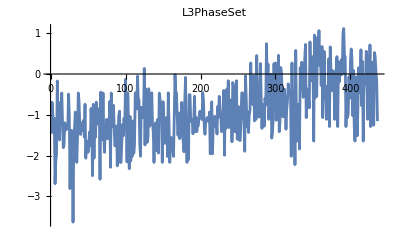
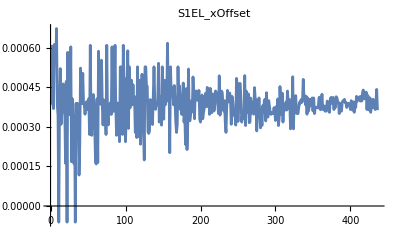
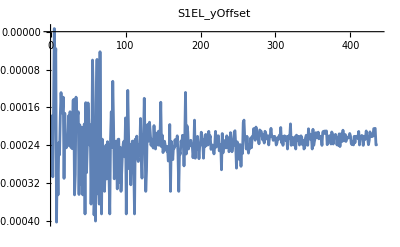
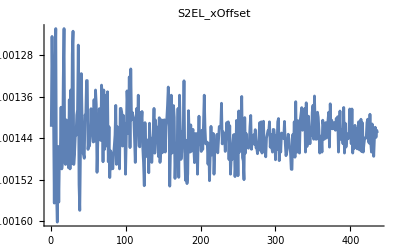
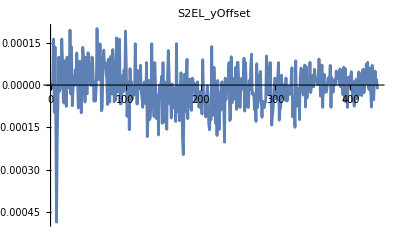
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | 0 | 0 | 0

```mathematica
imgArr=Table[
ListPlot[
raw[[All,key]],
PlotLabel->key,
ImageSize->400,
LabelStyle->15,
PlotRange->All,
Joined->True
],
{key,Keys[raw[[1]]]}
];

displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm
```

## Dump for symbolic regression

Open the CSV in excel, do the automatic suggestion, and resave

```mathematica
Export[
"~/srData.csv",
Dataset[raw]
]
```

~/srData.csv

## Linear model fit

```mathematica
freeVars=Intersection[
Keys[raw[[1]]],
{"L0BPhaseSet","L1PhaseSet","L2PhaseSet","L3PhaseSet","Q1EkG","Q2EkG","Q3EkG","Q4EkG","Q5EkG","Q6EkG","S1ELkG","S2ELkG","S3ELkG","S3ERkG","S2ERkG","S1ERkG","S1EL_xOffset","S1EL_yOffset","S2EL_xOffset","S2EL_yOffset","S2ER_xOffset","S2ER_yOffset","S1ER_xOffset","S1ER_yOffset","Q5FFkG","Q4FFkG","Q3FFkG","Q2FFkG","Q1FFkG","Q0FFkG", "XC1FFkG","XC3FFkG","YC1FFkG","YC2FFkG"}
]
(*Mathematica doesn't like underscores...*)
freeVarsMathematica=StringReplace[#,"_"->""]&/@freeVars;
```

{L0BPhaseSet,L1PhaseSet,L2PhaseSet,L3PhaseSet,S1EL_xOffset,S1EL_yOffset,S1ER_xOffset,S1ER_yOffset,S2EL_xOffset,S2EL_yOffset,S2ER_xOffset,S2ER_yOffset,XC1FFkG,XC3FFkG,YC1FFkG,YC2FFkG}

```mathematica
fitVar = "PDrive_sigmaSI90_z"
```

PDrive_sigmaSI90_z

```mathematica
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
]
```

FittedModel[…]

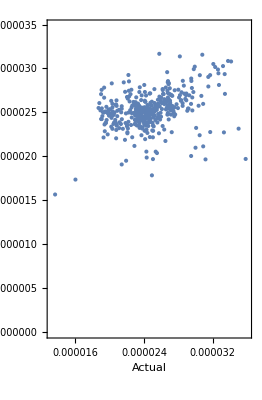

```mathematica
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
AspectRatio->Automatic,
Frame->True,
FrameLabel->{"Actual","Predicted"}
]
```

```mathematica
lm["ANOVATable"]
```

| DF | SS | MS | F-Statistic | P-Value
L0BPhaseSet | 1 | 2.94192×10^-12 | 2.94192×10^-12 | 0.173357 | 0.677359
L1PhaseSet | 1 | 5.80187×10^-11 | 5.80187×10^-11 | 3.41883 | 0.0651609
L2PhaseSet | 1 | 1.62857×10^-9 | 1.62857×10^-9 | 95.9659 | 1.53905×10^-20
L3PhaseSet | 1 | 4.85052×10^-13 | 4.85052×10^-13 | 0.0285824 | 0.865829
S1ELxOffset | 1 | 3.46125×10^-11 | 3.46125×10^-11 | 2.03959 | 0.153996
S1ELyOffset | 1 | 7.73752×10^-11 | 7.73752×10^-11 | 4.55944 | 0.0333172
S1ERxOffset | 1 | 6.63445×10^-11 | 6.63445×10^-11 | 3.90944 | 0.0486707
S1ERyOffset | 1 | 7.48659×10^-11 | 7.48659×10^-11 | 4.41157 | 0.0362931
S2ELxOffset | 1 | 1.98303×10^-11 | 1.98303×10^-11 | 1.16853 | 0.280326
S2ELyOffset | 1 | 1.49199×10^-10 | 1.49199×10^-10 | 8.79178 | 0.00319881
S2ERxOffset | 1 | 8.54189×10^-12 | 8.54189×10^-12 | 0.503343 | 0.47843
S2ERyOffset | 1 | 2.32751×10^-11 | 2.32751×10^-11 | 1.37152 | 0.242217
XC1FFkG | 1 | 9.568×10^-11 | 9.568×10^-11 | 5.63807 | 0.0180241
XC3FFkG | 1 | 1.92659×10^-10 | 1.92659×10^-10 | 11.3527 | 0.000823143
YC1FFkG | 1 | 7.96565×10^-15 | 7.96565×10^-15 | 0.000469387 | 0.982725
YC2FFkG | 1 | 1.91739×10^-15 | 1.91739×10^-15 | 0.000112985 | 0.991524
Error | 419 | 7.11057×10^-9 | 1.69703×10^-11 |  | 
Total | 435 | 9.54298×10^-9 |  |  |

### Fit all dependent vars

```mathematica
allFitVars  = Complement[
Keys[raw[[1]]],
freeVars
];
```

```mathematica
(*
imgArr=Table[
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
];

Show[
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
Frame->True,
FrameLabel->{"Actual","Predicted"},
PlotLabel->Row[{fitVar,": ",Style[ToString[lm["RSquared"]],ColorData["Rainbow"][lm["RSquared"]]]}],
ImageSize->400,
AspectRatio->1,
LabelStyle->15,
PlotRange->All
],
Plot[x,{x,Min[lm["Response"]],Max[lm["Response"]]},PlotStyle->Red]
],
{fitVar,allFitVars}
];*)
```

```mathematica
(*displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm*)
```

## Parse JSON strings to assoc

```mathematica
(*This is a stupid trick, but ensures numbers in scientific notation are interpreted correctly: https://mathematica.stackexchange.com/questions/15051/reading-in-scientific-notation-from-c-to-mathematica*)
stringToNumber[string_]:=ImportString[string,"Table"][[1,1]]
```

```mathematica
jsonTextToAssoc[string_]:=(
stringParts = StringSplit[StringDelete[#,WhitespaceCharacter],":"]&/@StringSplit[string,"\n"];
Association[#[[1]]->stringToNumber[#[[2]]]&/@stringParts]
)
```

```mathematica
tmp="L0BPhaseSet : -1.7210344516
L1PhaseSet : -20.3120443443
L2PhaseSet : -38.6737055166
L3PhaseSet : -1.4632882388
S1EL_xOffset : 0.0003852549
S1EL_yOffset : -0.0002411137
S2EL_xOffset : -0.0014178669
S2EL_yOffset : 0.0000111705
S2ER_xOffset : -0.002238162
S2ER_yOffset : -0.0006759962
S1ER_xOffset : 0.0010071369
S1ER_yOffset : 0.0003984557
XC1FFkG : 0.2064553639
XC3FFkG : -0.089916372
YC1FFkG : -0.0022311951
YC2FFkG : -0.0085115845";
```

```mathematica
priorSettings = jsonTextToAssoc[tmp]
```

<|L0BPhaseSet→-1.72103,L1PhaseSet→-20.312,L2PhaseSet→-38.6737,L3PhaseSet→-1.46329,S1EL_xOffset→0.000385255,S1EL_yOffset→-0.000241114,S2EL_xOffset→-0.00141787,S2EL_yOffset→0.0000111705,S2ER_xOffset→-0.00223816,S2ER_yOffset→-0.000675996,S1ER_xOffset→0.00100714,S1ER_yOffset→0.000398456,XC1FFkG→0.206455,XC3FFkG→-0.0899164,YC1FFkG→-0.0022312,YC2FFkG→-0.00851158|>

```mathematica
TableForm[
Table[
{
key,priorSettings[key],bestCase[key],bestCase[key]-priorSettings[key]
},
{key,Keys[priorSettings]}
],
TableHeadings->{None,{
Style["Parameter",Bold],
Style["150 μm spacing",Bold],
Style["200 μm spacing",Bold],
Style["Delta",Bold]}}
]
```

Parameter | 150 μm spacing | 200 μm spacing | Delta
L0BPhaseSet | -1.72103 | -1.91682 | -0.19579
L1PhaseSet | -20.312 | -19.752 | 0.560056
L2PhaseSet | -38.6737 | -38.8928 | -0.219119
L3PhaseSet | -1.46329 | -0.0680297 | 1.39526
S1EL_xOffset | 0.000385255 | 0.000415489 | 0.0000302345
S1EL_yOffset | -0.000241114 | -0.000220904 | 0.0000202097
S2EL_xOffset | -0.00141787 | -0.00142159 | -3.7247×10^-6
S2EL_yOffset | 0.0000111705 | 0.0000216812 | 0.0000105107
S2ER_xOffset | -0.00223816 | -0.00228295 | -0.0000447919
S2ER_yOffset | -0.000675996 | -0.000489676 | 0.00018632
S1ER_xOffset | 0.00100714 | 0.000901706 | -0.000105431
S1ER_yOffset | 0.000398456 | 0.000233506 | -0.00016495
XC1FFkG | 0.206455 | 0.207037 | 0.000581787
XC3FFkG | -0.0899164 | -0.09037 | -0.000453677
YC1FFkG | -0.0022312 | -0.00218319 | 0.0000480026
YC2FFkG | -0.00851158 | -0.00520243 | 0.00330915